## Exercises: Linear Regression

#### 1. The body mass index (BMI) and the systolic blood pressure of 6 people were measured to study a cardiovascular disease. The data are as follows: -Graphics- (a) The research hypothesis is that a high BMI relates to a high blood pressure. Estimate the linear model where blood pressure is the outcome and BMI is the covariate. Interpret the coefficients. (b) Calculate R^2 to judge the goodness of fit of the model.

```mathematica
SetDirectory[NotebookDirectory[]];
```

Solution to (a):

```mathematica
ClearAll["`*"]
```

```mathematica
data1={{26,170},{23,150},{27,160},{28,175},{24,155},{25,150}}
```

{{26,170},{23,150},{27,160},{28,175},{24,155},{25,150}}

```mathematica
lm1=LinearModelFit[data1,x,x]
```

FittedModel[…]

Interpretation of coefficients: A one-unit increase in the BMI relates to a 4.57 unit increase in the blood pressure. The model suggests a positive association between BMI and systolic blood pressure. It is impossible to have a BMI of 0; therefore, α cannot be interpreted meaningfully here.

Solution to (b):

```mathematica
lm1["RSquared"]
```

0.664935

Thus 66%of the data’s variability can be explained by the model. The goodness of fit is good, but not perfect.

#### 2. Consider the following data on weight and height of 17 female students: -Graphics- (a) Calculate the correlation coefficient of Bravais–Pearson. What does this imply with respect to a linear regression of height on weight? (b) Now estimate and interpret the linear regression model where “weight” is the outcome. Calculate R^2. (c) Predict the weight of a student with a height 175 cm. (d) Now produce a scatter plot of the data and interpret it. (e) Add the following two points to the scatter plot (x_18, y_18) = (175, 55) and (x_19, y_19) = (150, 75). Speculate how the linear regression estimate will change after adding these points. (f) Re-estimate the model using all 19 observations and calculate R^2 again. (g) Given the results of the two regression models: What are the general implications with respect to the least squares estimator of β?

Solution to (a):
(a) Calculate the correlation coefficient of Bravais–Pearson. What does this imply with respect to a linear regression of height on weight?

```mathematica
data2={{68,174},{58,164},{53,164},{60,165},{59,170},{60,168},{55,167},{62,166},{58,160},{53,160},{53,163},{50,157},{64,168},{77,179},{60,170},{63,168},{69,170}};
```

```mathematica
r=N[Correlation[data2[[;;,1]],data2[[;;,2]]]]
```

0.869996

From the correlation coefficient, we know that beta (slope of linear regression) must be equal to:

```mathematica
beta=r*Sqrt[Variance[data2[[;;,2]]]/Variance[data2[[;;,1]]]]
```

0.682616

Hence, for an increase of 1 kg in weight, we expect an increase of 0.68cm in height. Also, we know that:

```mathematica
R2=r^2
```

0.756894

Hence, we know that the fit of the linear regression model will be good.

Solution to (b):
(b) Now estimate and interpret the linear regression model where “weight” is the outcome. Calculate R^2.

First we swap the first and second column of the matrix containing the data:

```mathematica
data2swap[[All,{1,2}]]=data2[[All,{2,1}]]
```

Set::noval: Symbol data2swap in part assignment does not have an immediate value.

{{174,68},{164,58},{164,53},{165,60},{170,59},{168,60},{167,55},{166,62},{160,58},{160,53},{163,53},{157,50},{168,64},{179,77},{170,60},{168,63},{170,69}}

```mathematica
lm2=LinearModelFit[data2swap,x,x]
```

Each centimetre difference in height therefore means a 1.109 kg difference in weight. It is not possible to interpret the intercept meaningfully in this example.

Solution to (c):
(c) Predict the weight of a student with a height 175 cm.

```mathematica
lm2[175]
```

LinearModelFit[data2swap,x,x][175]

The prediction is 69.38 kg.

Solution to (d):
(d) Now produce a scatter plot of the data and interpret it.

```mathematica
ListPlot[data2swap,AxesLabel->{"height","weight"},PlotMarkers->{Automatic,12},LabelStyle->{FontSize->14}]
```

ListPlot::lpn: data2swap is not a list of numbers or pairs of numbers.

ListPlot[data2swap,AxesLabel→{height,weight},PlotMarkers→{Automatic,12},LabelStyle→{FontSize→14}]

There is clearly a positive association in that greater height implies greater weight. This is also emphasized by the regression line estimated in (b).

Solution to (e):
(e) Add the following two points to the scatter plot (x_18, y_18) = (175, 55) and (x_19, y_19) = (150, 75). Speculate how the linear regression estimate will change after adding these points.

```mathematica
newdata={{175,55},{150,75}}
```

{{175,55},{150,75}}

```mathematica
ListPlot[{newdata,data2swap},PlotMarkers->{Automatic,12},PlotStyle->{Red,Blue},AxesLabel->{"height","weight"},LabelStyle->{FontSize->14}]
```

-Graphics-

It is obvious that the two new data points do not match the pattern observed in the original 17 data points. One may therefore speculate that with the inclusion of the two new points beta will be smaller.

Solution to (f) and (g):
(f) Re-estimate the model using all 19 observations and calculate R^2 again.
(g) Given the results of the two regression models: What are the general implications with respect to the least squares estimator of β?

```mathematica
data2swapb=Append[data2swap,{175,55}];
```

Append::normal: Nonatomic expression expected at position 1 in Append[data2swap,{175,55}].

```mathematica
data2swapb=Append[data2swapb,{150,75}];
```

Append::argt: Append called with 3 arguments; 1 or 2 arguments are expected.

```mathematica
ListPlot[data2swapb,AxesLabel->{"height","weight"},PlotMarkers->{Automatic,12},LabelStyle->{FontSize->14}]
```

Append::argt: Append called with 3 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Append::argt will be suppressed during this calculation.

ListPlot::lpn: Append[data2swap,{175.,55.},{150.,75.}] is not a list of numbers or pairs of numbers.

ListPlot[Append[data2swap,{175,55},{150,75}],AxesLabel→{height,weight},PlotMarkers→{Automatic,12},LabelStyle→{FontSize→14}]

```mathematica
lm3=LinearModelFit[data2swapb,x,x]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Append[data2swap,{175,55},{150,75}],x,x]

```mathematica
lm3["RSquared"]
```

LinearModelFit[Append[data2swap,{175,55},{150,75}],x,x][RSquared]

This shows that the two added points shrink the estimate of beta from 1.109 to 0.276 . The association becomes less clear, with only 6.2% of the variability of the data explained by the linear regression model. This is an insightful example showing that least squares estimates are generally sensitive to outliers which can potentially affect the results .

#### 3. Consider the pizza delivery data. (a) Read the data and fit a multiple linear regression model with delivery time as the outcome and temperature, bill, number of ordered pizzas, and discount customer as covariates. Give a summary of the coefficients. (b) Add a quadratic polynomial of temperature to the model. (c) Estimate both R^2 and R^2adjusted for the model in (a) and the model in (b) and interpret the results. Plot in both cases the predicted versus the observed values.

Solution to (a):
(a) Read the data and fit a multiple linear regression model with delivery time as the outcome and temperature,  bill, number of ordered pizzas, and discount customer as covariates. Give a summary of the coefficients.

```mathematica
pizza=Import["pizza_delivery.csv"]
```

We first select the columns of interest:

```mathematica
data3=pizza[[2;;,{7,8,9,12,3}]];
```

```mathematica
lmpizza=LinearModelFit[data3,{temp,bill,np,disc},{temp,bill,np,disc}]
```

FittedModel[40.7912+0.163052 bill-0.383587 disc+0.643393 np-0.244787 temp]

```mathematica
Normal[lmpizza]
```

40.7912+0.163052 bill-0.383587 disc+0.643393 np-0.244787 temp

Interpretation of coefficients:
Bill (0.163052): For each additional EUR spent, the delivery time is expected to increase by approximately 0.163 minutes, holding all other variables constant.
Discount (-0.383587): If the customer received a discount, the delivery time is expected to decrease by approximately 0.384 minutes, holding all other variables constant.
Number of Pizzas: For each additional pizza in the order, the delivery time is expected to increase by approximately 0.643 minutes, holding all other variables constant.
Temperature at Delivery (-0.244787): For each additional degree in the temperature at delivery, the delivery time is expected to decrease by approximately 0.245 minutes, holding all other variables constant.

Solution to (b): 
(b) Add a quadratic polynomial of temperature to the model.

We first add a new column to the dataset, which is the squared of the temperature (remember it was on the first column of data3). Since we want the last column to be the outcome variable, we use Prepend and add the square of the temperature as the first column:

```mathematica
data3b=Map[Prepend[#,#[[1]]^2]&,data3];
```

Check result:

```mathematica
data3[[1;;2,;;]]
```

{{68.2877,58.4,4,1,35.1284},{70.9978,26.4,2,0,25.2031}}

```mathematica
data3b[[1;;2,;;]]
```

{{4663.21,68.2877,58.4,4,1,35.1284},{5040.69,70.9978,26.4,2,0,25.2031}}

```mathematica
lmpizza2=LinearModelFit[data3b,{temp2,temp,bill,np,disc},{temp2,temp,bill,np,disc}]
```

FittedModel[-24.3938+0.136709 bill-0.323275 disc+0.65382 np+1.89196 temp-0.0170164 temp2]

```mathematica
Normal[lmpizza2]
```

-24.3938+0.136709 bill-0.323275 disc+0.65382 np+1.89196 temp-0.0170164 temp2

Solution to (c):
(c) Estimate both R^2 and R^2adjusted for the model in (a) and the model in (b) and interpret the results. Plot in both cases the predicted versus the observed values.

```mathematica
R2={lmpizza["RSquared"],lmpizza2["RSquared"]}
```

{lmpizza[RSquared],lmpizza2[RSquared]}

```mathematica
R2adj={lmpizza["AdjustedRSquared"],lmpizza2["AdjustedRSquared"]}
```

{lmpizza[AdjustedRSquared],lmpizza2[AdjustedRSquared]}

```mathematica
AICpizza={lmpizza["AIC"],lmpizza2["AIC"]}
```

{lmpizza[AIC],lmpizza2[AIC]}

These results indicate that including the squared temperature as a covariate slightly  improves the fit, even though both models can only explain approximately 30% of the variability of the data.

We now calculate the predicted data by both models, by applying them to the corresponding input data:

```mathematica
pred1=lmpizza[Sequence@@#]&/@data3[[;;,{1,2,3,4}]];
```

```mathematica
pred2=lmpizza2[Sequence@@#]&/@data3b[[;;,{1,2,3,4,5}]];
```

Now we create data pairs containing the observed data and the predicted ones:

```mathematica
dataPairs1=Transpose[{data3[[;;,5]],pred1}];
```

```mathematica
dataPairs2=Transpose[{data3b[[;;,6]],pred2}];
```

Now we create the scatter plots and add the identity line for reference:

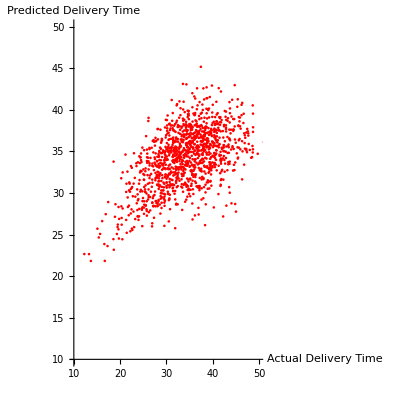

```mathematica
scatterPlot1=ListPlot[dataPairs1,AxesLabel->{"Actual Delivery Time","Predicted Delivery Time"},PlotStyle->Red,LabelStyle->{FontSize->14},AspectRatio->Automatic,PlotRange->{{10,50},{10,50}}]
```

We now determine the range for the plot:

```mathematica
allValues1=Flatten[dataPairs1];
minValue1=Min[allValues1];
maxValue1=Max[allValues1];
```

We now plot the identity line:

```mathematica
identityLine1=Plot[x,{x,minValue1,maxValue1},PlotStyle->{Blue,Dashed},AspectRatio->Automatic];
```

Now we combine the plots:

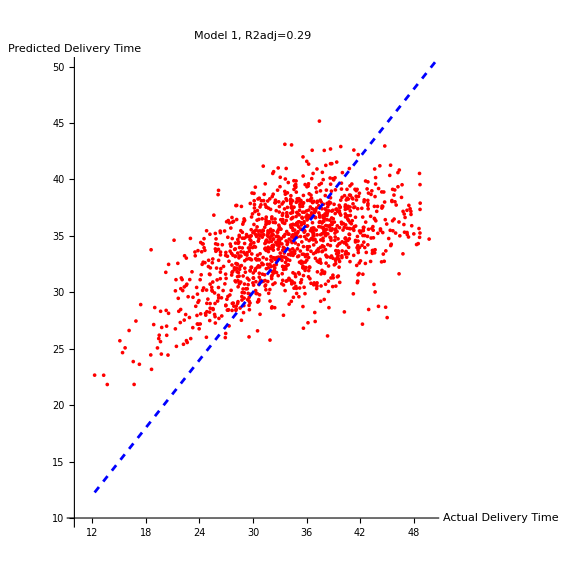

```mathematica
combinedPlot1=Show[scatterPlot1,identityLine1,ImageSize->Large,PlotLabel->Style["Model 1, R2adj=0.29",FontSize->16,Bold]]
```

We do the same for the second model:

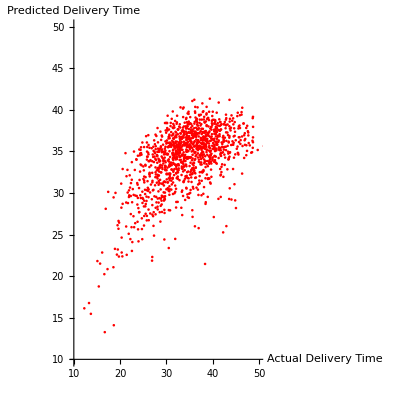

```mathematica
scatterPlot2=ListPlot[dataPairs2,AxesLabel->{"Actual Delivery Time","Predicted Delivery Time"},PlotStyle->Red,LabelStyle->{FontSize->14},AspectRatio->Automatic,PlotRange->{{10,50},{10,50}}]
```

We now determine the range for the plot:

```mathematica
allValues2=Flatten[dataPairs2];
minValue2=Min[allValues2];
maxValue2=Max[allValues2];
```

We now plot the identity line:

```mathematica
identityLine2=Plot[x,{x,minValue2,maxValue2},PlotStyle->{Blue,Dashed},AspectRatio->Automatic];
```

Now we combine the plots:

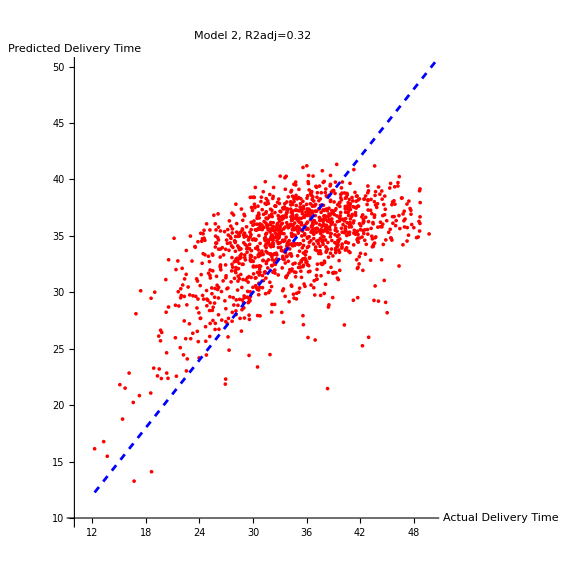

```mathematica
combinedPlot2=Show[scatterPlot2,identityLine2,ImageSize->Large,PlotLabel->Style["Model 2, R2adj=0.32",FontSize->16,Bold]]
```

Now for easier comparison, we plot the results for model 1 again below:

```mathematica
combinedPlot1
```

-Graphics-

Indeed, the points look closer to the identity line in the case of Model 2.